## Palm2015の実験結果の確認

```mathematica
Clear["Global`*"]
(*NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]*)
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"mathematica_plot_options.nb"}]]
```

plot2Doption

importData

jsonInfo

interpolateAndFourier

```mathematica
plot2Doption=Append[plot2Doption,{PlotStyle->{{Red},{Blue}}}];
plot2Doption=Append[plot2Doption,{GridLines->All}];
```

```mathematica
surgeExp=Import[FileNameJoin[{NotebookDirectory[],"surge.csv"}]];
tensionExp=Import[FileNameJoin[{NotebookDirectory[],"tension.csv"}]];
heaveExp=Import[FileNameJoin[{NotebookDirectory[],"heave.csv"}]];
pitchExp=Import[FileNameJoin[{NotebookDirectory[],"pitch.csv"}]];
waveelevationExp=Import[FileNameJoin[{NotebookDirectory[],"wave.csv"}]];
```

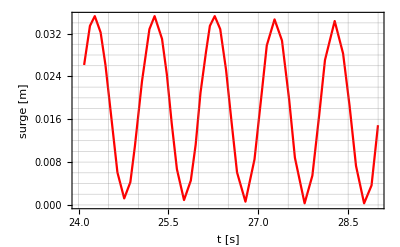
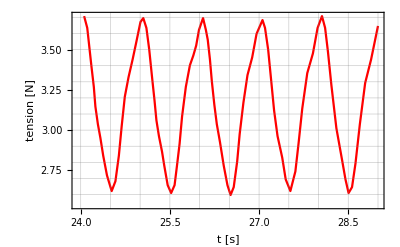
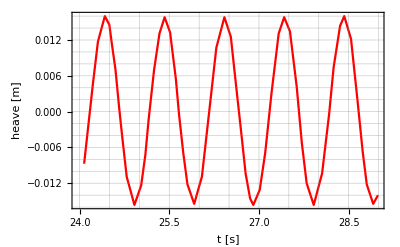
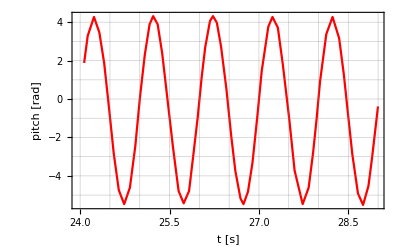
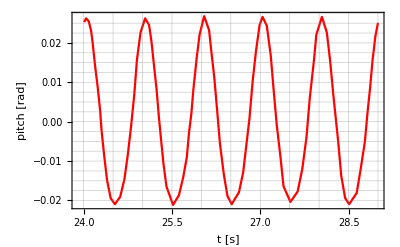

```mathematica
{ListPlot[surgeExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","surge [m]"}],
ListPlot[tensionExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","tension [N]"}],
ListPlot[heaveExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","heave [m]"}],
ListPlot[pitchExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}],
ListPlot[waveelevationExp,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","pitch [rad]"}]}
```

## 2. 実験結果と数値計算の比較

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json

/Users/tomoaki/BEM/Palm2016_with_mooring_H0d04_T1d0/result.json

no. | title | length
1 | cpu_time | 1688
2 | float_COM | 1688
3 | float_EK | 1688
4 | float_EP | 1688
5 | float_accel | 1688
6 | float_area | 1688
7 | float_drag_force | 1688
8 | float_drag_torque | 1688
9 | float_force | 1688
10 | float_pitch | 1688
11 | float_roll | 1688
12 | float_torque | 1688
13 | float_velocity | 1688
14 | float_yaw | 1688
15 | probe1_intersection | 1688
16 | probe2_intersection | 1688
17 | probe3_intersection | 1688
18 | probe4_intersection | 1688
19 | simulation_time | 1688
20 | wall_clock_time | 1688
21 | water_E | 1688
22 | water_EK | 1688
23 | water_EP | 1688
24 | water_face_size | 1688
25 | water_point_size | 1688
26 | water_volume | 1688

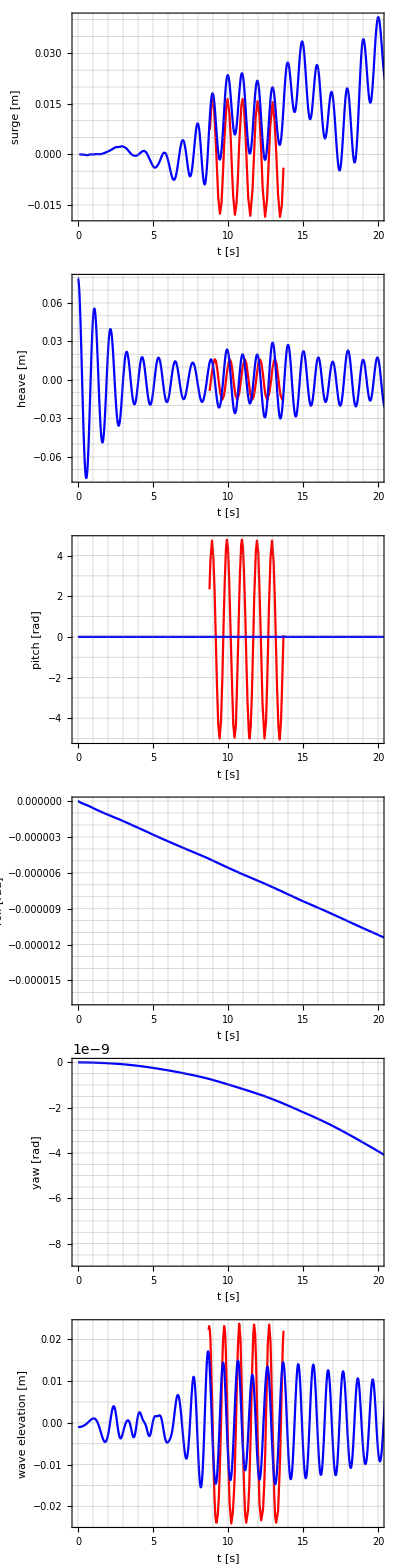

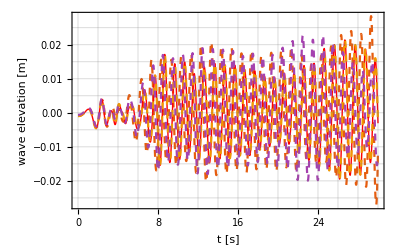

```mathematica
nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"
nameSim="/Users/tomoaki/BEM/Palm2016_with_mooring_H0d04_T1d0/result.json"
(*nameSim="/Users/tomoaki/BEM/Palm2016_coarse_with_mooring_H0d04_T1d0/result.json"*)
(*nameSim="~/BEM/Palm2016_with_mooring/result.json"*)
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

probe1=importData[nameSim,"probe1_intersection"][[;;,3]];
probe1-=Mean[%];
probe2=importData[nameSim,"probe2_intersection"][[;;,3]];
probe2-=Mean[%];
probe3=importData[nameSim,"probe3_intersection"][[;;,3]];
probe3-=Mean[%];
probe4=importData[nameSim,"probe4_intersection"][[;;,3]];
probe4-=Mean[%];



istar=15;
shift=15.3;
maxtime=20;

Column@{ListPlot[{{#1-shift,#2-Mean[surgeExp[[;;,2]]]}&@@@surgeExp,Transpose@{time[[istar;;]],surgeSim[[istar;;]]}},
PlotRange->{{0,maxtime},Automatic},
Joined->True,Evaluate[plot2Doption],
FrameLabel->{"t [s]","surge [m]"}],
ListPlot[{{#1-shift,#2-Mean[heaveExp[[;;,2]]]}&@@@heaveExp,Transpose@{time,heaveSim-Mean[heaveSim]}},
PlotRange->{{0,maxtime},Automatic},
Joined->True,Evaluate[plot2Doption],
FrameLabel->{"t [s]","heave [m]"}],
ListPlot[{{#1-shift,#2-Mean[pitchExp[[;;,2]]]}&@@@pitchExp,Transpose@{time,pitchSim-Mean[pitchSim]}},
PlotRange->{{0,maxtime},All},
Joined->True,
Evaluate[plot2Doption],
FrameLabel->{"t [s]","pitch [rad]"}],
ListPlot[Transpose@{time,rollSim},
PlotRange->{{0,maxtime},Automatic},
Joined->True,
PlotStyle->Blue,
Evaluate[plot2Doption],
FrameLabel->{"t [s]","roll [rad]"}],
ListPlot[Transpose@{time,yawSim},
PlotRange->{{0,maxtime},Automatic},
Joined->True,
PlotStyle->Blue,
Evaluate[plot2Doption],
FrameLabel->{"t [s]","yaw [rad]"}],
ListPlot[{{#1-shift,#2-Mean[waveelevationExp[[;;,2]]]}&@@@waveelevationExp,Transpose@{time,probe2}},
PlotRange->{{0,maxtime},Automatic},
Joined->True,Evaluate[plot2Doption],
FrameLabel->{"t [s]","wave elevation [m]"}]}

ListPlot[{{time,probe1}ᵀ,{time,probe2}ᵀ,{time,probe3}ᵀ,{time,probe4}ᵀ}
,PlotStyle->{{Automatic,Dashed},{Thick,Red},{Automatic,Dashed},{Automatic,Dashed},{Automatic,Dashed}}
,Joined->True,Evaluate[plot2Doption],FrameLabel->{"t [s]","wave elevation [m]"}]
```

### 2.2 フーリエ解析

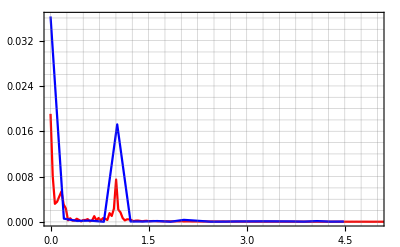

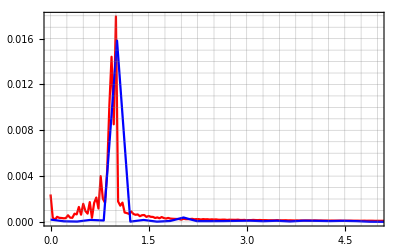

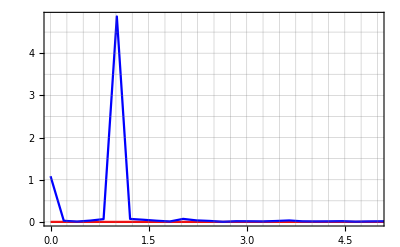

```mathematica
ListPlot[{interpolateAndFourier[time[[istar;;]],surgeSim[[istar;;]]],
interpolateAndFourier[surgeExp[[2;;,1]],surgeExp[[2;;,2]]]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
ListPlot[{interpolateAndFourier[time,heaveSim-0.725],
interpolateAndFourier[heaveExp[[2;;,1]],heaveExp[[2;;,2]]]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
ListPlot[{interpolateAndFourier[time,pitchSim-Mean[pitchSim]],
interpolateAndFourier[pitchExp[[2;;,1]],pitchExp[[2;;,2]]]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
```

## 係留ありとなしの比較（数値計算）

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_without_mooring/result.json

no. | title | length
1 | cpu_time | 1481
2 | float_COM | 1481
3 | float_EK | 1481
4 | float_EP | 1481
5 | float_accel | 1481
6 | float_area | 1481
7 | float_drag_force | 1481
8 | float_drag_torque | 1481
9 | float_force | 1481
10 | float_pitch | 1481
11 | float_roll | 1481
12 | float_torque | 1481
13 | float_velocity | 1481
14 | float_yaw | 1481
15 | probe1_intersection | 1481
16 | probe2_intersection | 1481
17 | probe3_intersection | 1481
18 | probe4_intersection | 1481
19 | simulation_time | 1481
20 | wall_clock_time | 1481
21 | water_E | 1481
22 | water_EK | 1481
23 | water_EP | 1481
24 | water_face_size | 1481
25 | water_point_size | 1481
26 | water_volume | 1481

/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json

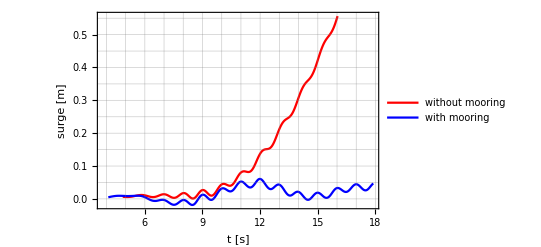
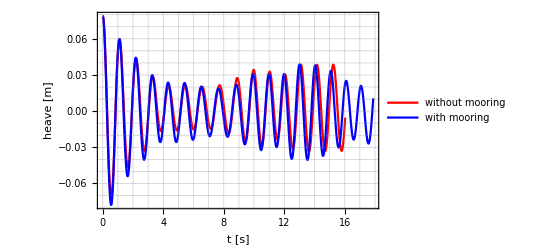
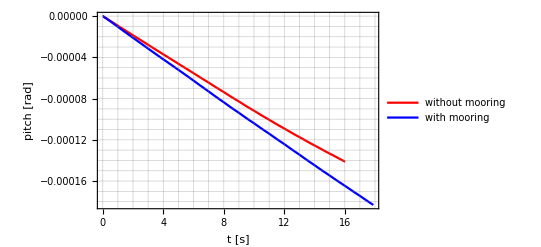
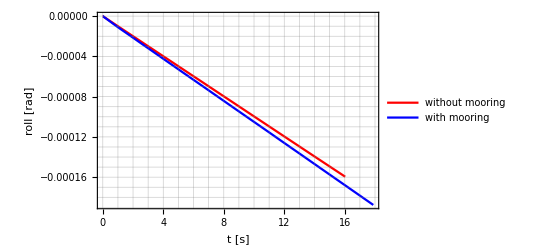
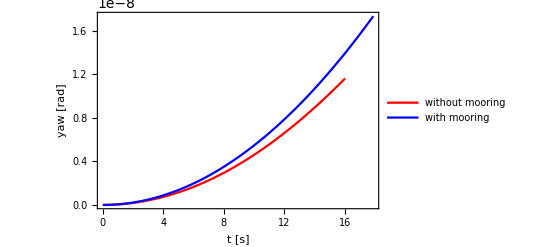

```mathematica
nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_without_mooring/result.json"

(*nameSim="~/BEM/Palm2016_with_mooring/result.json"*)
jsonInfo[nameSim]

time=importData[nameSim,"simulation_time"];
surgeSim=importData[nameSim,"float_COM",1]-6;
heaveSim=importData[nameSim,"float_COM",3];
forceSim=importData[nameSim,"float_force"];
pitchSim=importData[nameSim,"float_pitch"];
rollSim=importData[nameSim,"float_roll"];
yawSim=importData[nameSim,"float_yaw"];
torqueSim=importData[nameSim,"float_torque"];

nameSim="/Volumes/home/BEM/202403土木学会東北支部玉津/Palm2016_with_mooring/result.json"
timeMoor=importData[nameSim,"simulation_time"];
surgeSimMoor=importData[nameSim,"float_COM",1]-6;
heaveSimMoor=importData[nameSim,"float_COM",3];
forceSimMoor=importData[nameSim,"float_force"];
pitchSimMoor=importData[nameSim,"float_pitch"];
rollSimMoor=importData[nameSim,"float_roll"];
yawSimMoor=importData[nameSim,"float_yaw"];
torqueSimMoor=importData[nameSim,"float_torque"];

opt={PlotStyle->{Red,Blue},PlotLegends->{"without mooring","with mooring"}};
opt=AppendTo[opt,plot2Doption];

istart=400;

{ListPlot[{Transpose@{time[[istart;;]],surgeSim[[istart;;]]},Transpose@{timeMoor[[istart;;]],surgeSimMoor[[istart;;]]}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","surge [m]"}],
ListPlot[{Transpose@{time,heaveSim-0.725},Transpose@{timeMoor,heaveSimMoor-0.725}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","heave [m]"}],
ListPlot[{Transpose@{time,pitchSim},Transpose@{timeMoor,pitchSimMoor}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","pitch [rad]"}],
ListPlot[{Transpose@{time,rollSim},Transpose@{timeMoor,rollSimMoor}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","roll [rad]"}],
ListPlot[{Transpose@{time,yawSim},Transpose@{timeMoor,yawSimMoor}},Joined->True,Evaluate[opt],FrameLabel->{"t [s]","yaw [rad]"}]}
```

### 3.2 フーリエ解析

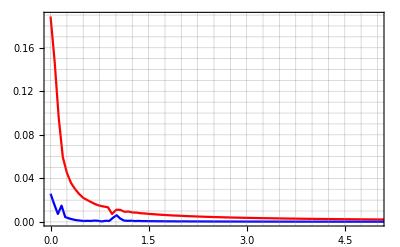

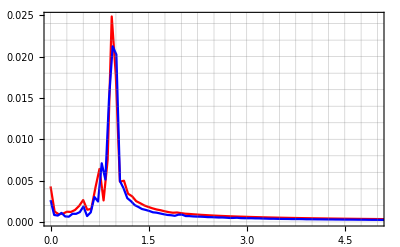

```mathematica
ListPlot[{
interpolateAndFourier[time[[istar;;]],surgeSim[[istar;;]]],
interpolateAndFourier[timeMoor[[istar;;]],surgeSimMoor[[istar;;]]]},
PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]

ListPlot[{
interpolateAndFourier[time,heaveSim-0.725],
interpolateAndFourier[timeMoor,heaveSimMoor-0.725]},PlotRange->{{0,5},All},Joined->True,Evaluate[plot2Doption]]
```